```mathematica
v="9";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/GapD-l5k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/velD-l5k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/AveVel-l5k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/GapD-l10k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/velD-l10k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/AveVel-l10k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/GapD-l20k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/velD-l20k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/AveVel-l20k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number}];
```

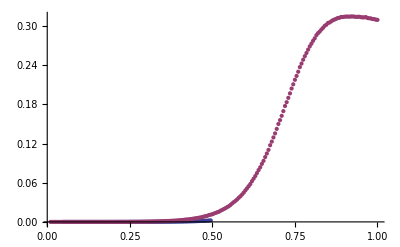

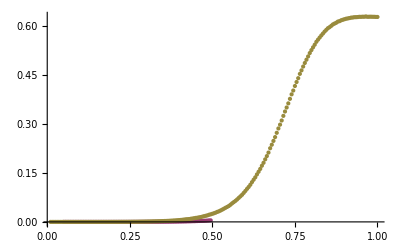

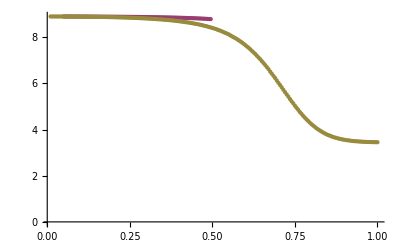

```mathematica
v="9";
p="0.1";

g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/GapD-l5k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/velD-l5k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/AveVel-l5k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/GapD-l10k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/velD-l10k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/AveVel-l10k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/GapD-l20k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
v20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/velD-l20k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
av20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/AveVel-l20k-v"<>v<>"-p0.1obc.txt",{Number,Number,Number,Number}];
ngap="4";
nvel="4";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
ClearAll[d0,z,α];
d0=0.0674;
z=0.65;
α=0.65;
gap5v9=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g5k1]}];
vel5v9=Table[{v5k1[[All,1]][[j]],Sum[v5k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v5k1]}];
avel5v9=Table[{av5k1[[All,1]][[j]],av5k1[[All,2]][[j]]},{j,1,Length[av5k1]}];
gap10v9=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g10k1]}];
vel10v9=Table[{v10k1[[All,1]][[j]],Sum[v10k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v10k1]}];
avel10v9=Table[{av10k1[[All,1]][[j]],av10k1[[All,2]][[j]]},{j,1,Length[av10k1]}];
gap20v9=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[g20k1]}];
vel20v9=Table[{v20k1[[All,1]][[j]],Sum[v20k1[[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[v20k1]}];
avel20v9=Table[{av20k1[[All,1]][[j]],av20k1[[All,2]][[j]]},{j,1,Length[av20k1]}];
ListPlot[{gap10v9,gap20v9,gap5v9},PlotRange->Full]
ListPlot[{vel5v9,vel10v9,vel20v9},PlotRange->Full]
ListPlot[{avel5v9,avel10v9,avel20v9},PlotRange->Full]
```

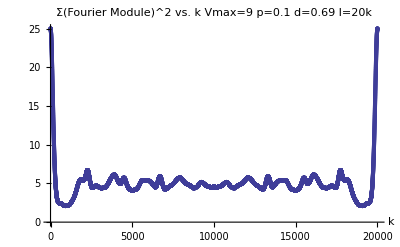

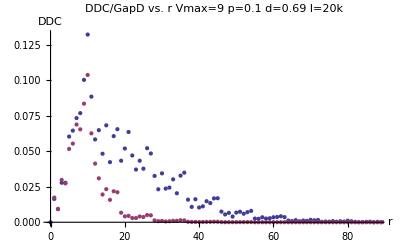

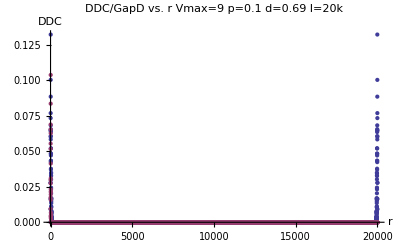

```mathematica
d="0.69";
l="20";
v="9";
p="0.1";
fourier=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/Fourier1D-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>"obc.txt",{Number,Number}];
ddc=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/DDC-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>"obc.txt",{Number,Number}];
gf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/GapDFull-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>"obc.txt",{Number,Number}];
nc=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/test/NumCar-d"<>d<>"-l"<>l<>"k-v"<>v<>"-p"<>p<>"obc.txt",{Number,Number}];
jj=StringToStream[v];
vmax= Read[jj,Number];
dif=Table[{i,ddc[[All,2]][[i]]-gf[[All,2]][[i]]},{i,1,vmax-1}];
ListPlot[fourier,PlotLabel->"Σ(Fourier Module)^2 vs. k Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"k"," "},PlotRange->Full]
ListPlot[{ddc,gf},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->{{0,88},Full}]
ListPlot[{ddc,gf},PlotLabel->"DDC/GapD vs. r Vmax="<>v<>"  p="<>p<>" d="<>  d<>" l="<>l<>"k",AxesLabel->{"r","DDC"},PlotRange->Full]
```

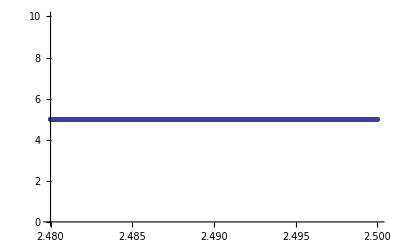

```mathematica
ListPlot[nc]
```